Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

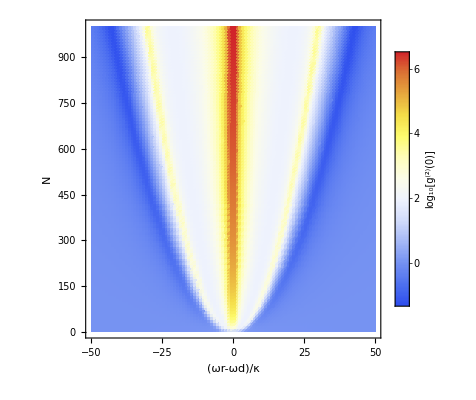

```mathematica
Clear["Global`*"];
CloseKernels[];
LaunchKernels[200];

data=ParallelTable[
ωr=5.69*2*Pi;
ωge=5.69*2*Pi;


g=0.0135*2*Pi;
γeg=0.0000763*2*Pi;
κ=0.01*2*Pi;
F=1.5*κ;


max1=50*κ;
min1=-50*κ;      (*max and min value of Δ*)
segment1=100;
max2=1001;
min2=1;
segment2=100;
Δ=N[min1+(max1-min1)*(m-1)/segment1];(*m is the variable of Δ for circulation*)
(*Δ=ωr-ωd*)
Na=IntegerPart[max2-(max2-min2)*((s-1)/segment2)];
C1=√((4*F^2*Δ^2)/(8*F^4+4 (Na*g^2-Δ^2)^2+8*F^2*(Na*g^2+Δ^2)+Δ^2 κ^2));
ωgedeviation=10^-3*ωge;
deltadatage=RandomReal[NormalDistribution[ωge,ωgedeviation],Na]-ωge;
sumdeltage=Sum[deltadatage[[i]],{i,Na}];
equs=Table[{Δ*ToExpression[StringJoin["Ce1",ToString[i]]]+C2*√2*g-I/2*κ*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce1",ToString[i]]]+F*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce1",ToString[i]]]==0,g*C1+F*ToExpression[StringJoin["Ce1",ToString[i]]]-I/2*γeg*ToExpression[StringJoin["Ce0",ToString[i]]]+Δ*ToExpression[StringJoin["Ce0",ToString[i]]]==0},{i,1,Na}];
equs=Flatten[equs];
equs=Append[equs,2*Δ*C2+F*C1*√2-I*κ*C2+g*(Sum[ToExpression[StringJoin["Ce1",ToString[i]]],{i,Na}])*√2==0];


vars={C2,Table[ToExpression[StringJoin["Ce1",ToString[i]]],{i,1,Na}],Table[ToExpression[StringJoin["Ce0",ToString[i]]],{i,1,Na}]};
vars=Flatten[vars];
S=NSolve[equs,vars];
C2data=C2/.S[[1,1]];
Ce1data=Table[ToExpression[StringJoin["Ce1",ToString[i]]]/.S[[1,i+1]],{i,1,Na}];

logg20=Chop[Log10[2/(C1*Conjugate[C1])*(C2data/C1)*(Conjugate[C2data]/Conjugate[C1])]];


{Δ/κ,Na,logg20},{m,1,100+1,1},{s,1,100+1,1},Method->"FinestGrained"

];
(*Circulation is ended.*)


data3Dflatten=Flatten[data,1];
ListDensityPlot[data3Dflatten,FrameLabel->{"(ωr-ωd)/κ","N"},ColorFunction->"TemperatureMap",BaseStyle->{FontSize->16,FontFamily->"Calibri"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10[g^(2)(0)]",LabelStyle->{FontSize->16,FontFamily->"Calibri"}],Right]]
```

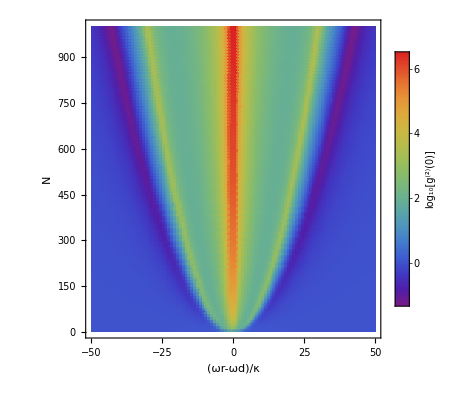

```mathematica
ListDensityPlot[data3Dflatten,FrameLabel->{"(ωr-ωd)/κ","N"},ColorFunction->"Rainbow",BaseStyle->{FontSize->16,FontFamily->"Calibri"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10[g^(2)(0)]",LabelStyle->{FontSize->16,FontFamily->"Calibri"}],Right]]
```

```mathematica
Export["/home/u000011703749/CircuitJ-Cdesityplot.txt",data3Dflatten,"Table"];
```

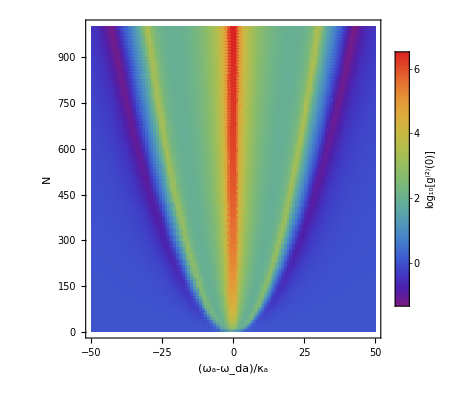
```mathematica
Export["/home/u000011703749/fig4a.eps",-Graphics-]
```

/home/u000011703749/fig4a.eps

```mathematica
data3Dflatten=Import["/home/u000011703749/CircuitJ-Cdesityplot.txt","Table"];
ListDensityPlot[data3Dflatten,FrameLabel->{"(ω_a-ω_da)/κ_a","N"},ColorFunction->"Rainbow",BaseStyle->{FontSize->20,FontFamily->"Calibri"},PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"log_10[g^(2)(0)]",LabelStyle->{FontSize->20,FontFamily->"Calibri"}],Right]]
```

-Graphics-